## Settings

```mathematica
imgsize=700;
```

```mathematica
eqn = D[D[f[x],x],x]-( a k Cot[k x]+i(omegam - a Sin[k x]Cos[2thetam]) a Sin[k x] )D[f[x],x]+(Sin[2 thetam]/2)^2 a^2 Sin[k x]^2 f[x]==0
```

1/4 a^2 f[x] Sin[2 thetam]^2 Sin[k x]^2-(a k Cot[k x]+a i Sin[k x] (omegam-a Cos[2 thetam] Sin[k x])) f'[x]+f''[x]==0

```mathematica
DSolve[eqn,f[x],x]
```

DSolve[1/4 a^2 f[x] Sin[2 thetam]^2 Sin[k x]^2-(a k Cot[k x]+a i Sin[k x] (omegam-a Cos[2 thetam] Sin[k x])) f'[x]+f''[x]==0,f[x],x]

```mathematica
DSolve[f[x]+x D[f[x],x]==omegam/2-deltalambda[x]Sin[2thetam]/2,f[x],x]
```

{{f[x]→C[1]/x+(∫_1^x 1/2 (omegam-deltalambda[K[1]] Sin[2 thetam])ⅆK[1])/x}}

```mathematica
sys=I D[{phi1[x],phi2[x]},x]=={{0,(g0R+I g0I) Exp[I(-omegam+n0 k)x]},{(g0R-I g0I) Exp[-I(-omegam+n0 k)x],0}}.{phi1[x],phi2[x]}
```

{ⅈ phi1'[x],ⅈ phi2'[x]}=={ⅇ^(ⅈ (k n0-omegam) x) (ⅈ g0I+g0R) phi2[x],ⅇ^(-ⅈ (k n0-omegam) x) (-ⅈ g0I+g0R) phi1[x]}

```mathematica
DSolve[sys,{phi1,phi2},x]
```

{{phi1→Function[{x},ⅇ^(1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) C[1]+ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x) C[2]],phi2→Function[{x},1/(2 (g0I-ⅈ g0R))ⅈ ⅇ^(-ⅈ (k n0-omegam) x+1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) C[1]+1/(2 (g0I-ⅈ g0R))ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x-ⅈ (k n0-omegam) x) (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) C[2]]}}

```mathematica
%//FullSimplify
```

{{phi1→Function[{x},ⅇ^(1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) C[1]+ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x) C[2]],phi2→Function[{x},1/(2 (g0I-ⅈ g0R))ⅈ ⅇ^(-ⅈ (k n0-omegam) x+1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) C[1]+1/(2 (g0I-ⅈ g0R))ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x-ⅈ (k n0-omegam) x) (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) C[2]]}}

## Understand The Hamiltonian

```mathematica
ClearAll[k,x,phi,function1,constant1]
DSolve[I D[function1[x],x]==constant1 Sin[k x+phi]function1[x],function1,x]//FullSimplify
```

{{function1→Function[{x},ⅇ^(-ⅈ constant1 (-(Cos[phi] Cos[k x])/k+(Sin[phi] Sin[k x])/k)) C[1]]}}

```mathematica
ClearAll[a,k,x,phi,function1,constant1]
DSolve[D[D[function1[x],x],x]-D[a Sin[k x + phi],x]/(a Sin[k x + phi])D[function1[x],x]==-Sin[2thetam]^2/4(a Sin[k x + phi])^2 function1[x],function1,x]
```

{{function1→Function[{x},C[1] Cos[(a Cos[phi+k x] Sin[2 thetam])/(2 k)]-C[2] Sin[(a Cos[phi+k x] Sin[2 thetam])/(2 k)]]}}

## Constant Matter ‘Perturbation’

```mathematica
ClearAll[k,x,phi,function1,function2,constant1]
DSolve[I D[{function1[x],function2[x]},x]==Sin[2thetam]/2 lambdac{{0,Exp[I Cos[2thetam]lambdac x-I omegam x]},{Exp[-I Cos[2thetam]lambdac x + I omegam x],0}}.{function1[x],function2[x]},{function1,function2},x]//FullSimplify
```

{{function1→Function[{x},ⅇ^(-1/2 ⅈ x (omegam-lambdac Cos[2 thetam]-ⅈ √(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[1]+ⅇ^(1/2 x (ⅈ (-omegam+lambdac Cos[2 thetam])+√(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[2]],function2→Function[{x},1/lambdac ⅇ^(ⅈ omegam x-ⅈ lambdac x Cos[2 thetam]-1/2 ⅈ x (omegam-lambdac Cos[2 thetam]-ⅈ √(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[1] (omegam-lambdac Cos[2 thetam]-ⅈ √(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam])) Csc[2 thetam]+1/lambdac ⅈ ⅇ^(ⅈ omegam x-ⅈ lambdac x Cos[2 thetam]+1/2 x (ⅈ (-omegam+lambdac Cos[2 thetam])+√(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[2] (ⅈ (-omegam+lambdac Cos[2 thetam])+√(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam])) Csc[2 thetam]]}}

## Investigate Resonance

Define the amplitude

```mathematica
ClearAll[khat,ahat,thetam,thetamV,zk,n0,x,phi,function1,function2,constant1]
```

```mathematica
thetamV=Pi/5;
aV=1;
phiV=0;
```

```mathematica
fun[khat_,ahat_,thetam_,n0_]=1/4 ahat Sin[2thetam](2n0+1)/zk BesselJ[n0,zk]/.{zk->ahat/khat Cos[2thetam]}
(* In RWA, n0->Round[1/khat] *)
```

1/4 khat (1+2 n0) BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]

```mathematica
amplitude[khat_,ahat_,thetam_,n0_] = (4 Abs[fun[khat,ahat,thetam,n0]]^2)/(4 Abs[fun[khat,ahat,thetam,n0]]^2+(n0 khat - 1)^2)/.{zk->ahat/khat Cos[2thetam]}
(* In RWA, n0->Round[1/khat] *)
```

Abs[khat (1+2 n0) BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]]^2/(4 ((-1+khat n0)^2+1/4 Abs[khat (1+2 n0) BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]]^2))

```mathematica
(*Limit[amplitude[k,a,t,Round[k]],k->Infinity]*)
```

```mathematica
Limit[amplitude[k,a,t,Round[k]],t->0]
(*Limit[amplitude[k,a,t],t->Pi/4]*)
```

0

```mathematica
Table[{amplitude[k,0.1,Pi/5,Round[k]],k},{k,0.1,1,0.1}]
```

{{0.0220716,0.1},{0.0855853,0.2},{0.174914,0.3},{0.274182,0.4},{0.371417,0.5},{0.0307993,0.6},{0.0534823,0.7},{0.112806,0.8},{0.33715,0.9},{1.,1.}}

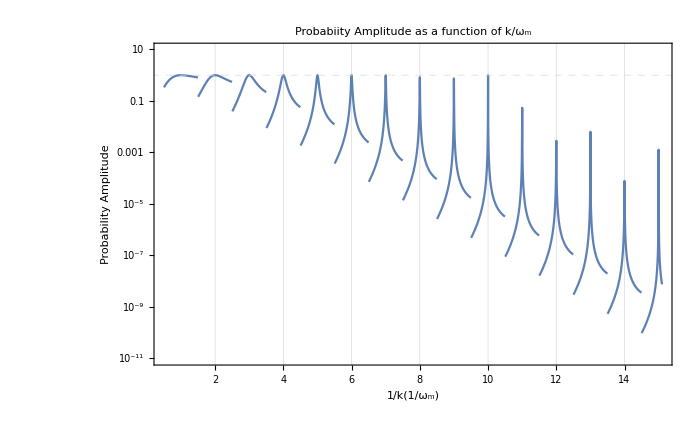

```mathematica
LogPlot[amplitude[1/k,aV,thetamV,Round[k]],{k,0.5,15.1},ImageSize->imgsize,Frame->True,PlotRange->Full,GridLines->{Automatic,{1}},GridLinesStyle->Directive[Thin,Dashed],FrameLabel->{"1/k(1/ω_m)","Probability Amplitude"},PlotLabel->"Probabiity Amplitude as a function of k/ω_m"]
```

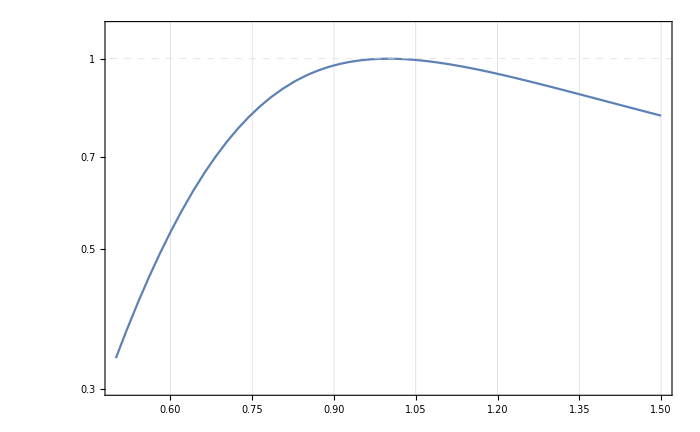

```mathematica
LogPlot[amplitude[1/k,aV,thetamV,Round[k]],{k,0.5,1.5},ImageSize->imgsize,Frame->True,PlotRange->Full,GridLines->{Automatic,{1}},GridLinesStyle->Directive[Thin,Dashed]]
```

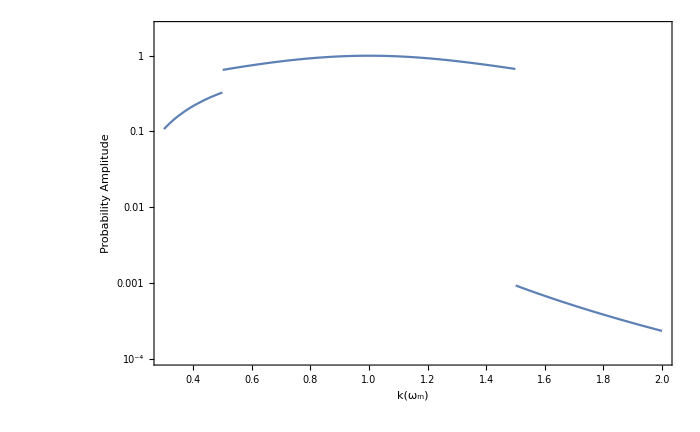

```mathematica
LogPlot[amplitude[k,aV,thetamV,Round[k]],{k,0.3,2},FrameLabel->{"k(ω_m)","Probability Amplitude"},ImageSize->imgsize,Frame->True,PlotRange->Full]
```

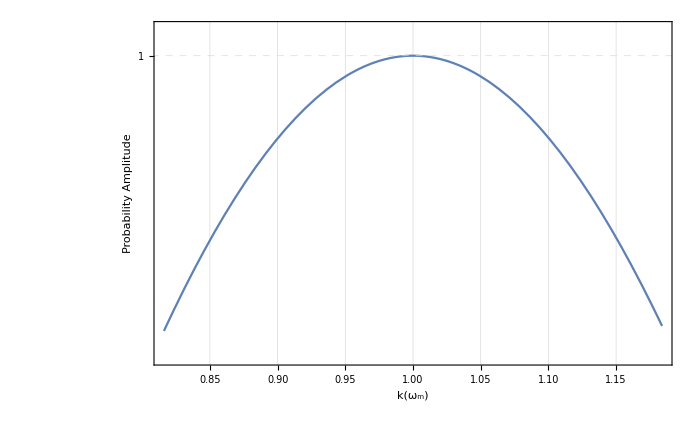
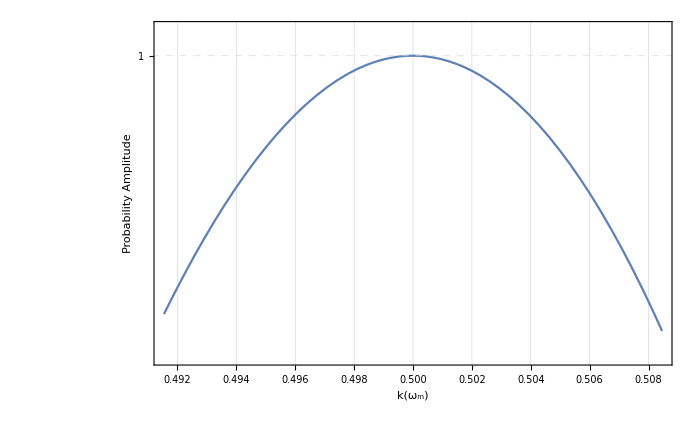
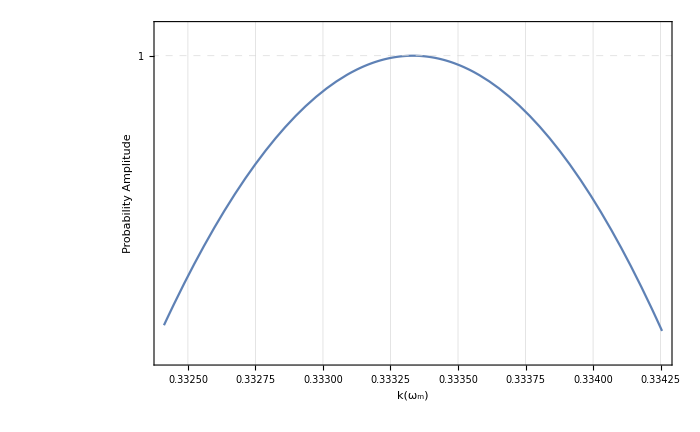
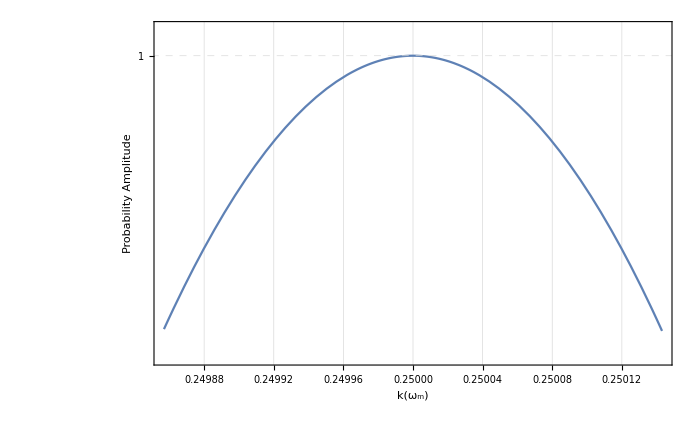

```mathematica
Table[LogPlot[amplitude[k,aV,thetamV,n],{k,(1-0.5/Exp[n]/n^2)/n,(1+0.5/Exp[n]/n^2)/n},FrameLabel->{"k(ω_m)","Probability Amplitude"},ImageSize->imgsize,Frame->True,PlotRange->Full,GridLines->{Automatic,{1}},GridLinesStyle->Directive[Thin,Dashed]],{n,1,4}]
```

```mathematica
Series[BesselJ[0,x],{x,0,3}]
```

1-x^2/4+O[x]^4

```mathematica
Limit[BesselJ[0,x]/x,x->0]
```

∞

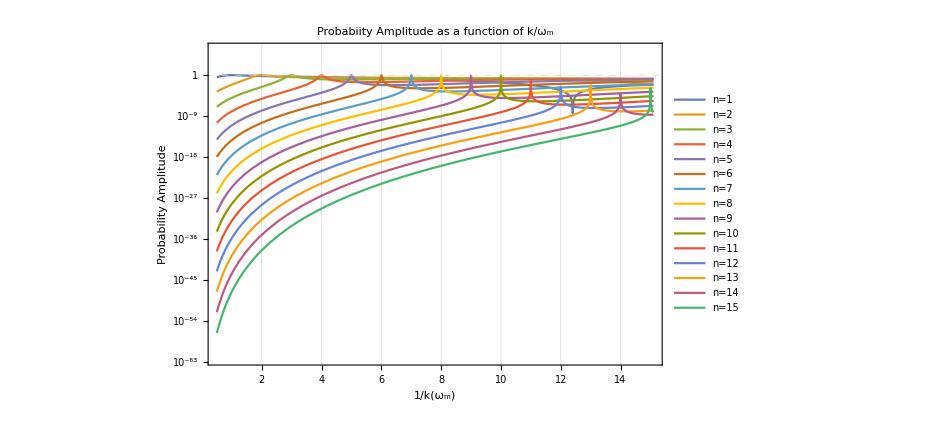

```mathematica
listFunctions=Table[amplitude[1/k,aV,thetamV,n],{n,1,15,1}];
listFunctionsLegends=Table["n="<>ToString@n,{n,1,15,1}];
LogPlot[listFunctions,{k,0.5,15.1},ImageSize->imgsize,Frame->True,PlotRange->Full,GridLines->{Automatic,{1}},GridLinesStyle->Directive[Thin,Dashed],FrameLabel->{"1/k(ω_m)","Probability Amplitude"},PlotLabel->"Probabiity Amplitude as a function of k/ω_m",PlotLegends->listFunctionsLegends]
```

### Investigation on Width

Looking for the width

```mathematica
aWV=0.01
endpointWList=10
```

0.01

10

```mathematica
fwhm[n_]:=First@Differences[k/.{ToRules@Reduce[amplitude[k,aWV,thetamV, n] == 0.5&&k>(1-1/n)/n&&k<(1+1/n)/n, k]}]
fwhmRange[n_]:=First@Differences[k/.{ToRules@Reduce[amplitude[k,aWV,thetamV, n] == 0.5&&k>(1-0.5/Exp[n]/n^2)/n&&k<(1+0.5/Exp[n]/n^2)/n, k]}]
fwhmFR[n_]:=2*(k - n) /. FindRoot[amplitude[k,aWV,thetamV, n] == 0.5, {k,1/n,(1-0.5/Exp[n]/n^2)/n,(1+0.5/Exp[n]/n^2)/n}];
```

```mathematica
fwhm[1]
fwhmRange[1]
fwhm[2]
```

0.0142658

0.0142658

0.0000183682

```mathematica
widthList=Table[{i,fwhmRange[i]},{i,1,endpointWList}] (*For pertubation amplitude equals 0.1*)
(*widthList=Table[{i,fwhm[i]},{i,1,endpointWList}]*) (*For large perturbation amplitude*)
widthListLog=Table[{widthList[[i,1]],Log@widthList[[i,2]]},{i,1,endpointWList}];
widthLine=Fit[widthListLog,{1,x},x];(*Fit data of {x,Log[y]}*)
```

{{1,0.0142658},{2,0.0000183682},{3,3.97326×10^-8},{4,1.0524×10^-10},{5,First[{}]},{6,9.71445×10^-16},{7,First[{}]},{8,First[{}]},{9,First[{}]},{10,First[{}]}}

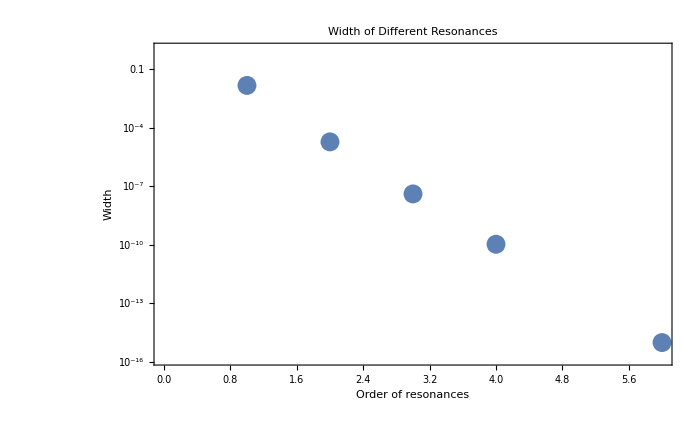

```mathematica
widthListPlt=ListLogPlot[widthList,ImageSize->imgsize,Frame->True,FrameLabel->{"Order of resonances","Width"},PlotLabel->"Width of Different Resonances"]
```

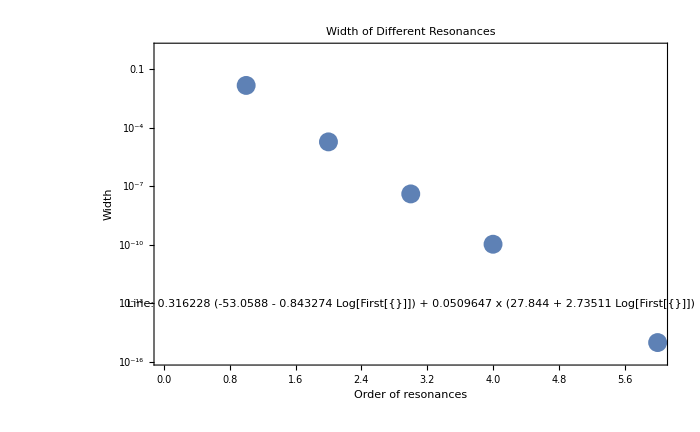

```mathematica
widthLinePlt=Plot[widthLine,{x,1,10},ImageSize->imgsize,Frame->True];
Show[widthListPlt,widthLinePlt,Epilog->Inset[Framed[Style["Line: "<>ToString[widthLine],20],Background->White],{3,-30}]]
```

#### Lorentzian Approximation?

The amplitude has a F^2/(F^2+g^2) form, we assume the bessel function dosn’t change a lot during the resonance. Thus we have the width

```mathematica
widthLor[thetam_,ahat_,n0_]:=N@ahat Sin[2thetam](2n0+1)/(ahat n0 Cos[2thetam])BesselJ[n0,ahat n0 Cos[2thetam]]
```

```mathematica
widthLor[thetamV,aWV,1]
```

0.0142658

```mathematica
widthLorList=Table[{i,widthLor[thetamV,aWV,i]},{i,1,10}]
```

{{1,0.0142658},{2,0.0000367365},{3,1.19198×10^-7},{4,4.20961×10^-10},{5,1.55265×10^-12},{6,5.87895×10^-15},{7,2.26534×10^-17},{8,8.83881×10^-20},{9,3.48111×10^-22},{10,1.381×10^-24}}

```mathematica
widthDiffList=Table[{i,(widthList[[i,2]]-widthLorList[[i,2]])/widthList[[i,2]]},{i,1,10}]
```

{{1,-1.82203×10^-10},{2,-1.},{3,-2.},{4,-3.},{5,(-1.55265×10^-12+First[{}])/First[{}]},{6,-5.05176},{7,(-2.26534×10^-17+First[{}])/First[{}]},{8,(-8.83881×10^-20+First[{}])/First[{}]},{9,(-3.48111×10^-22+First[{}])/First[{}]},{10,(-1.381×10^-24+First[{}])/First[{}]}}

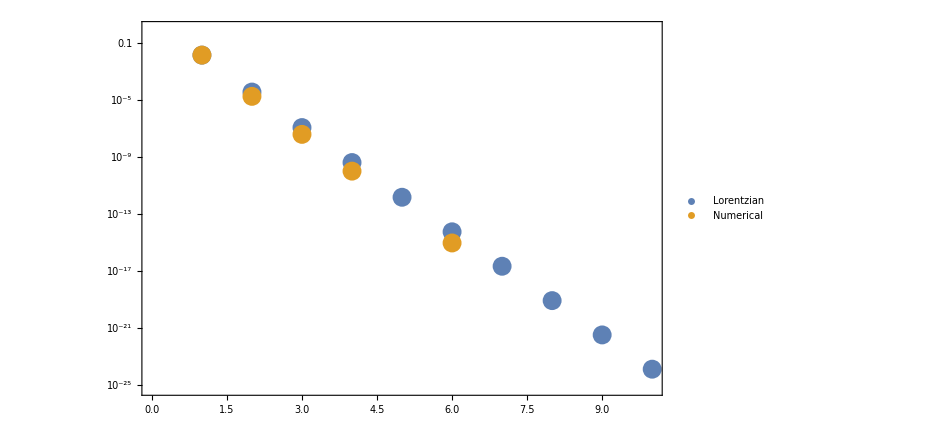

```mathematica
ListLogPlot[{widthLorList,widthList},PlotLegends->{"Lorentzian","Numerical"},Frame->True,ImageSize->imgsize]
ListPlot[widthDiffList,PlotRange->Full];
```

#### What is Bessel Function

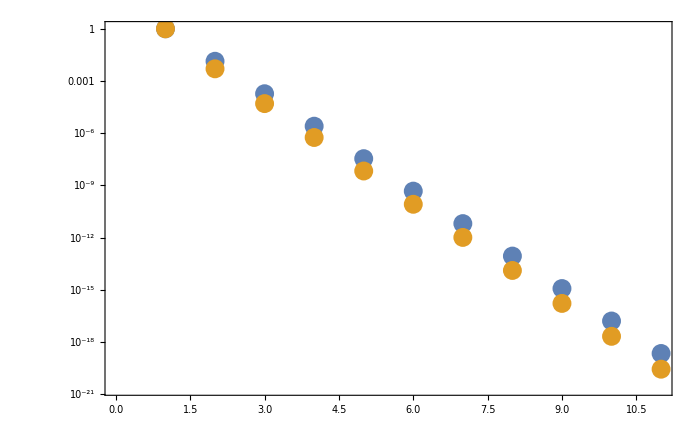

```mathematica
delta=0.01;
besselJApprox[n_]:=Exp[n](delta/2)^n;
ListLogPlot[{Table[besselJApprox[n],{n,0,10}],Table[BesselJ[n,n*delta],{n,0,10}]},Frame->True,ImageSize->imgsize]
```

## 2-frequency system

```mathematica
ClearAll[k1,k2,x,phi1,phi2,psi1,psi2,lambdac,h,h0,sol0,bFun,phase,a1,a2,h12,h12A,h12B,h12C,h12D,,hA,hB,hC,hD,h12C,h12C,sol0,solA,solB,solC,solD]
```

Endpoint for NDSolve

```mathematica
endpoint=200
```

200

```mathematica
bFun[n1_,n2_,zk1_,zk2_,thetam_]:=Sin[2thetam]/4(-(-I)^(n1+n2))(2n1+1)/zk1 BesselJ[n1,zk1]BesselJ[n2,zk2]
phase[n1_,n2_,phi1_,phi2_]:=Exp[I(n1 phi1+n2 phi2)]
```

```mathematica
h1[n1_,n2_,n1p_,n2p_,k1_,k2_,a1_,a2_,zk1_,zk2_,phi1_,phi2_,thetam_,x_]:=a1 bFun[n1,n2p,zk1,zk2,thetam]phase[n1,n2p,phi1,phi2]Exp[I(n1 k1+n2p k2-1)x]
h2[n1_,n2_,n1p_,n2p_,k1_,k2_,a1_,a2_,zk1_,zk2_,phi1_,phi2_,thetam_,x_]:=a2 bFun[n2,n1p,zk2,zk1,thetam]phase[n1p,n2,phi1,phi2]Exp[I(n1p k1+n2 k2-1)x]
```

I have n1 =1, n2=1, n1p=Round[(n2 k2 - 1)/k1], n2p=Round[(n1 k1 - 1)/k2],

```mathematica
thetamV=Pi/5;
k1V=0.95;
k2V=k1V*2.1;
n1pV=Round[(n2V k2V-1)/k1V];
n2pV=Round[(n1V k1V-1)/k2V];
a1V=0.1;
a2V=0.000000001;
zk1V=a1V Cos[2thetamV]/k1V;
zk2V=a2V Cos[2thetamV]/k2V;
phi1V=0;
phi2V=0;
init={psi1[0],psi2[0]}=={1,0};
```

```mathematica
n101=Round[1/k1V];
n201=Round[(1-n101 k1V)/k2V];
n202=Round[1/k2V];
n102=Round[(1-n202 k2V)/k1V];
n1p1=n101+1;
n2p1=Round[(1-n1p1 k1V)/k2V];
n2p2=n201+1;
n1p2=Round[(1-n2p2 k2V)/k1V];
n1m1=n101-1;
n2m1=Round[(1-n1m1 k1V)/k2V];
n2m2=n202-1;
n1m2=Round[(1-n2m2 k1V)/k2V];
```

Solve the complete hamiltonian

```mathematica
h0[k1_,k2_,a1_,a2_,phi1_,phi2_,thetam_,x_]:=(a1 Sin[k1 x+phi1]+a2 Sin[k2 x+phi2])Sin[2thetam]Exp[2I(-x/2-Cos[2thetam]/2(a1/k1 Cos[k1 x+phi1]+a2/k2 Cos[k2 x+phi2]))];
```

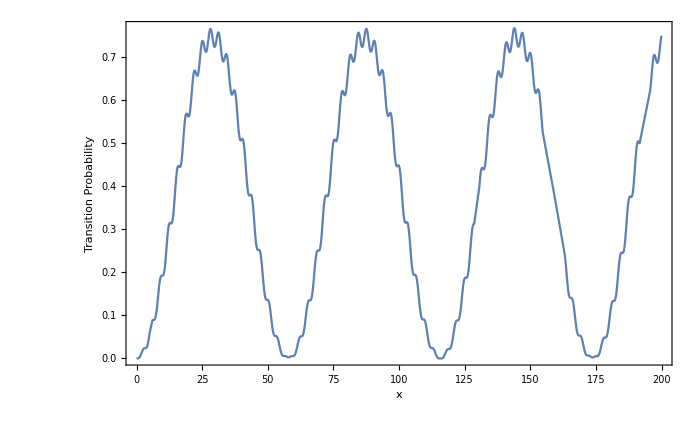

```mathematica
sol0=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h0[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x]},{Conjugate[h0[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}];

plt0=Plot[Evaluate[Abs[psi2[x]]^2/.sol0],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"}]
```

Include only the “most important” term in the series

```mathematica
h[n1_,n2_,n1p_,n2p_,k1_,k2_,a1_,a2_,zk1_,zk2_,phi1_,phi2_,thetam_,x_]:=h1[n1,n2,n1p,n2p,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]+h2[n1,n2,n1p,n2p,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]
```

```mathematica
(*zk=a Cos[2 thetam]/k*)
```

```mathematica
h12[k1_,k2_,a1_,a2_,phi1_,phi2_,thetam_,x_]:=h[n1V,n2V,n1pV,n2pV,k1,k2,a1,a2,zk1V,zk2V,phi1,phi2,thetam,x]
(*h[1,1,Round[( k2-1)/k1],Round[(k1-1)/k2],k1,k2,a1,a2,a1 Cos[2thetam]/k1,a2 Cos[2thetam]/k2,phi1,phi2,thetam,x]*)
```

```mathematica
(*DSolve[I D[{psi1[x],psi2[x]},x]=={{0,h12[k1,k2,a1,a2,phi1,phi2,thetam,x]},{Conjugate[h12[k1,k2,a1,a2,phi1,phi2,thetam,x]],0}}.{psi1[x],psi2[x]},{psi1,psi2},x]//FullSimplify*)
```

```mathematica
Re@h12[0.95,1.03,0.1,0.2,0,0,Pi/5,4] (*Test the function*)
Re@h12[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,4]
```

0.00625861

0.00708453

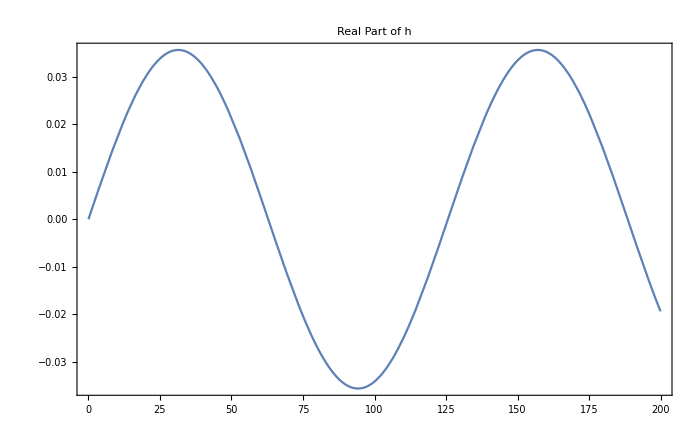

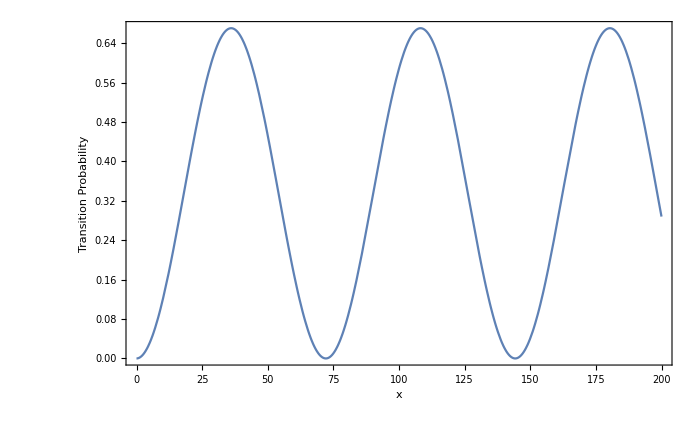

```mathematica
pltARe=Plot[Re[h12[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x]],{x,0,endpoint},Frame->True,ImageSize->imgsize,PlotLabel->"Real Part of h"]

h12A[x_]:=h12[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x];

solA=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h12A[x]},{Conjugate[h12A[x]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}];

pltA=Plot[Evaluate[Abs[psi2[x]]^2/.solA],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"}]
```

#### Higher Order Series

Add only higher terms to see the interference of first term (interference from the first frequency resonance)

```mathematica
hB[n1_,n2_,n1p_,n2p_,k1_,k2_,a1_,a2_,zk1_,zk2_,phi1_,phi2_,thetam_,x_]:=h1[n1,n2,n1p,n2p,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]+h2[n1,n2,n1p,n2p,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]+h1[n1,n2,n1p,n2p+1,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]+
h1[n1,n2,n1p,n2p-1,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]
```

```mathematica
h12B[k1_,k2_,a1_,a2_,phi1_,phi2_,thetam_,x_]:=hB[n1V,n2V,n1pV,n2pV,k1,k2,a1,a2,zk1V,zk2V,phi1,phi2,thetam,x];

pltBRe=Plot[Re[h12B[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x]],{x,0,endpoint},Frame->True,ImageSize->imgsize,PlotLabel->"Real Part of h"]

ClearAll[psi1,psi2]

h12B[x_]:=h12B[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x];
solB=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h12B[x]},{Conjugate[h12B[x]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}];

pltB=Plot[Evaluate[Abs[psi2[x]]^2/.solB],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"}]
```

-Graphics-

-Graphics-

Add only higher terms to see the interference of second term (interference from the second frequency resonance)

```mathematica
hC[n1_,n2_,n1p_,n2p_,k1_,k2_,a1_,a2_,zk1_,zk2_,phi1_,phi2_,thetam_,x_]:=h1[n1,n2,n1p,n2p,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]+h2[n1,n2,n1p,n2p,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]+h2[n1,n2,n1p+1,n2p,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]+
h2[n1,n2,n1p-1,n2p,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]
```

-Graphics-

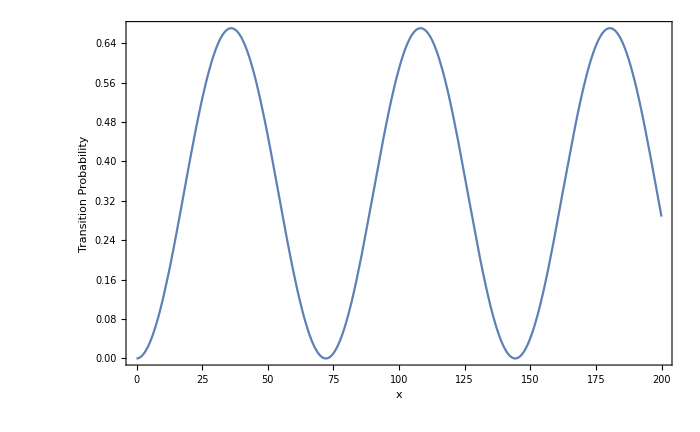

```mathematica
h12C[k1_,k2_,a1_,a2_,phi1_,phi2_,thetam_,x_]:=hC[n1V,n2V,n1pV,n2pV,k1,k2,a1,a2,zk1V,zk2V,phi1,phi2,thetam,x];

pltCRe=Plot[Re[h12C[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x]],{x,0,endpoint},Frame->True,ImageSize->imgsize,PlotLabel->"Real Part of h"]

ClearAll[psi1,psi2]

h12C[x_]:=h12C[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x];
solC=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h12C[x]},{Conjugate[h12C[x]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}];

pltC=Plot[Evaluate[Abs[psi2[x]]^2/.solC],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"}]
```

Add both higher terms to see the interference of first term (interference from the first frequency resonance) and second term

```mathematica
hD[n1_,n2_,n1p_,n2p_,k1_,k2_,a1_,a2_,zk1_,zk2_,phi1_,phi2_,thetam_,x_]:=h1[n1,n2,n1p,n2p,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]+h2[n1,n2,n1p,n2p,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]+h1[n1,n2,n1p,n2p+1,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]+
h1[n1,n2,n1p,n2p-1,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]+h2[n1,n2,n1p+1,n2p,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]+
h2[n1,n2,n1p-1,n2p,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]
```

-Graphics-

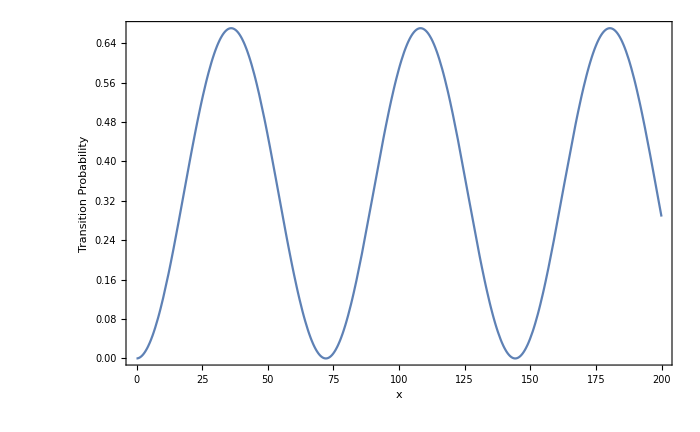

```mathematica
h12D[k1_,k2_,a1_,a2_,phi1_,phi2_,thetam_,x_]:=hD[n1V,n2V,n1pV,n2pV,k1,k2,a1,a2,zk1V,zk2V,phi1,phi2,thetam,x];

pltDRe=Plot[Re[h12D[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x]],{x,0,endpoint},Frame->True,ImageSize->imgsize,PlotLabel->"Real Part of h"]

h12D[x_]:=h12D[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x];

ClearAll[psi1,psi2]

solD=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h12D[x]},{Conjugate[h12D[x]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}];

pltD=Plot[Evaluate[Abs[psi2[x]]^2/.solD],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"}]
```

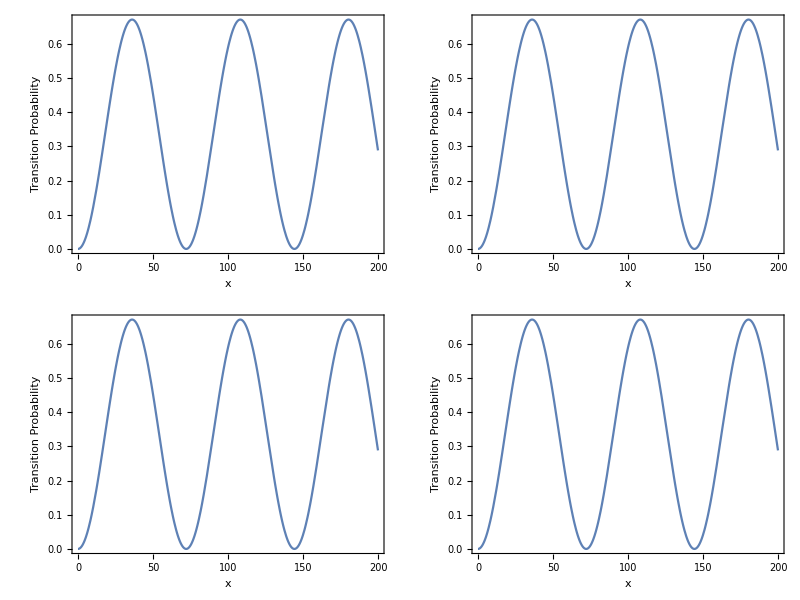

```mathematica
Grid[{{pltA,pltB},{pltC,pltD}}]
(*A:lowest order;B:more h1;C:more h2;D:both h1 and h2 higher order*)
```

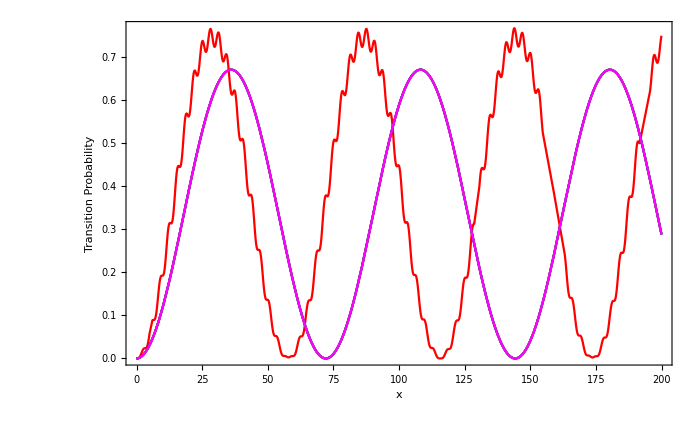

```mathematica
col0=Cases[plt0,_RGBColor,Infinity][[1]];
colA=Cases[pltA,_RGBColor,Infinity][[1]];
colB=Cases[pltB,_RGBColor,Infinity][[1]];
colC=Cases[pltC,_RGBColor,Infinity][[1]];
colD=Cases[pltD,_RGBColor,Infinity][[1]];
Show[plt0/.col0->Red,pltA/.colA->Blue,pltB/.colB->Black,pltC/.colC->Gray,pltD/.colD->Magenta]
(*A:lowest order;B:more h1;C:more h2;D:both h1 and h2 higher order*)
```

## Analytical Analysis

```mathematica
Series[BesselJ[n,x],{x,n a Cos[2thetam],3}]//FullSimplify
```

BesselJ[n,a n Cos[2 thetam]]+(-BesselJ[1+n,a n Cos[2 thetam]]+(BesselJ[n,a n Cos[2 thetam]] Sec[2 thetam])/a) (x-a n Cos[2 thetam])+1/(2 a^2 n)(a BesselJ[1+n,a n Cos[2 thetam]] Sec[2 thetam]-BesselJ[n,a n Cos[2 thetam]] (a^2 n-(-1+n) Sec[2 thetam]^2)) (x-a n Cos[2 thetam])^2+1/(6 a^3 n^2)(-1/2 (-1+n) BesselJ[n,a n Cos[2 thetam]] (4+(-2+a^2) n+a^2 n Cos[4 thetam]) Sec[2 thetam]^3+a BesselJ[1+n,a n Cos[2 thetam]] (a^2 n^2-(2+n^2) Sec[2 thetam]^2)) (x-a n Cos[2 thetam])^3+O[x-a n Cos[2 thetam]]^4

```mathematica
Series[1/(k0+k1),{k1,0,3}]
```

1/k0-k1/k0^2+k1^2/k0^3-k1^3/k0^4+O[k1]^4

```mathematica
Series[((1-n0 k1 +n0^2k1^2))^(2m+n),{k1,0,2}]//FullSimplify
```

1-(2 m+n) n0 k1+1/2 (2 m+n) (1+2 m+n) n0^2 k1^2+O[k1]^3

```mathematica
fterm=1/2 Tan[2thetam](2n+1)(1/n+k1)(bes0-bes1 k1+bes2 k1^2);
Collect[fterm^2,k1]
```

1/4 bes2^2 k1^6 (1+2 n)^2 Tan[2 thetam]^2+1/4 k1 (-(2 bes0 bes1)/n^2+(2 bes0^2)/n) (1+2 n)^2 Tan[2 thetam]^2+1/4 k1^2 (bes0^2+bes1^2/n^2+(2 bes0 bes2)/n^2-(4 bes0 bes1)/n) (1+2 n)^2 Tan[2 thetam]^2+1/4 k1^3 (-2 bes0 bes1-(2 bes1 bes2)/n^2+(2 bes1^2)/n+(4 bes0 bes2)/n) (1+2 n)^2 Tan[2 thetam]^2+1/4 k1^4 (bes1^2+2 bes0 bes2+bes2^2/n^2-(4 bes1 bes2)/n) (1+2 n)^2 Tan[2 thetam]^2+1/4 k1^5 (-2 bes1 bes2+(2 bes2^2)/n) (1+2 n)^2 Tan[2 thetam]^2+(bes0^2 (1+2 n)^2 Tan[2 thetam]^2)/(4 n^2)

```mathematica
gterm=n(1/n+k1)-1;
Collect[gterm^2,k1]
```

k1^2 n^2

```mathematica
Solve[c0+c1 x+(c2-n^2) x^2==0,x]
```

{{x→(-c1-√(c1^2-4 c0 c2+4 c0 n^2))/(2 (c2-n^2))},{x→(-c1+√(c1^2-4 c0 c2+4 c0 n^2))/(2 (c2-n^2))}}

```mathematica
testNDep[c0_,c1_,c2_,n_]:=(√(c1^2-4c0(c2-n^2)))/(c2-n^2)
```

```mathematica
Manipulate[Plot[testNDep[c0,c1,c2,n],{n,1,10}],{c0,0,1},{c1,0,1},{c2,0,1}]
```